```mathematica
(*grades, anonymized, post-first stage processing*)
grades={{5,5,5,4,2},{5,5,1,5,0},{4,4,2,4,1},{4,3,2,3,1},{4,4,1,5,1},{4,4,4,4,0},{5,5,5,5,2},{5,5,3,2,0},{4,5,5,4,0},{5,3,4,5,1}};
```

```mathematica
(*messy way to take Transpose of grades & include test total scores*)
p1={};
p2={};
p3={};
p4={};
p5={};
total={};
For[i=1,i≤Length[grades],i++,
p1=Append[p1,grades[[i]][[1]]];
p2=Append[p2,grades[[i]][[2]]];
p3=Append[p3,grades[[i]][[3]]];
p4=Append[p4,grades[[i]][[4]]];
p5=Append[p5,grades[[i]][[5]]];
total=Append[total,Sum[grades[[i]][[k]],{k,1,5}]];
]
score={p1,p2,p3,p4,p5,total};
```

```mathematica
(*compute correlation matrix*)
corr=ConstantArray[0,{6,6}];
For[i=1,i≤6,i++,
For[j=1,j≤6,j++,
corr[[i]][[j]]=N[Correlation[score[[i]],score[[j]]]];
]
]
```

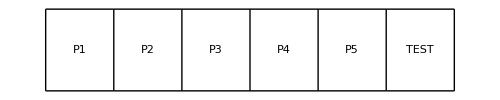
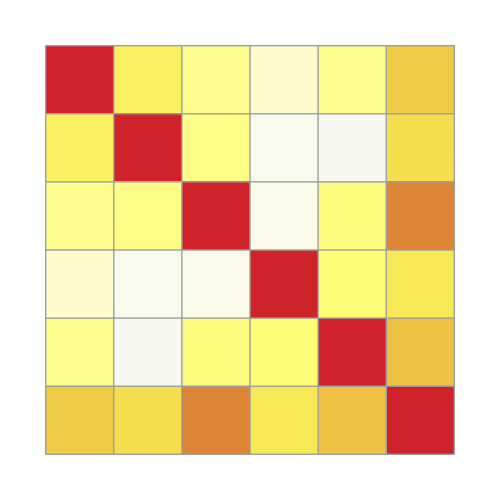
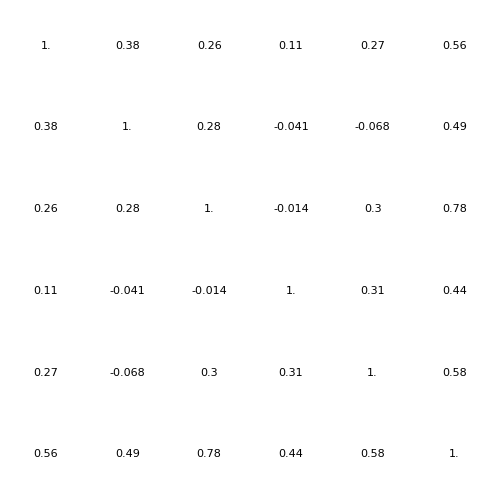
-Graphics-
-Graphics--Graphics--Graphics-

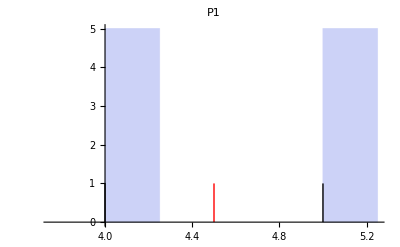
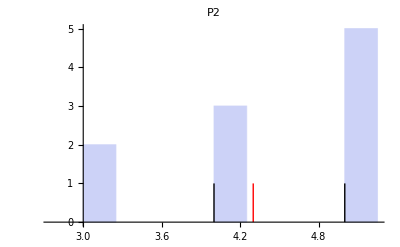
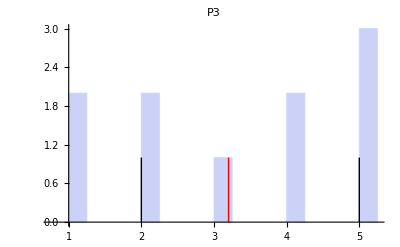
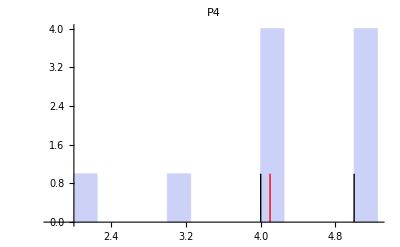
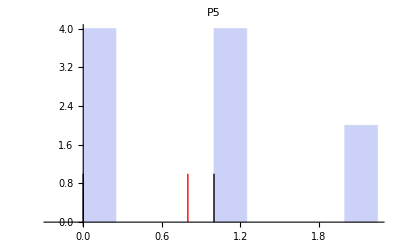
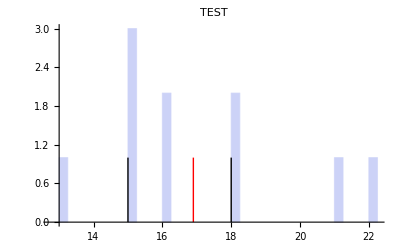

-Graphics-

```mathematica
(*labels for the correlation array*)
labels={P1,P2,P3,P4,P5,TEST};
(*Fancy picture*)
Column[{GraphicsRow[labels,ImageSize->500,Frame->All],Row[{GraphicsColumn[labels,ImageSize->83,Frame->All],Overlay[{ArrayPlot[corr,ColorFunction->(ColorData["TemperatureMap"][(1+#)/2]&),Frame->None,Mesh->True,PlotRangePadding->0,ImageSize->500,ColorFunctionScaling->False],GraphicsGrid[Map[NumberForm[#,2]&,corr,{2}],ImageSize->500]}]}]},Alignment->Right,Spacings->0]
(*histograms,for,each,problem,&,test,as,a,whole*)
histograms={};
For[i=1,i≤6,i++,
histograms=Append[histograms,Histogram[score[[i]],{.25},Epilog->{Directive[{Thick,Red}],Line[{{Mean[score[[i]]],0},{Mean[score[[i]]],1}}],{Directive[{Thick,Black}],Line[{{Quartiles[score[[i]]][[1]],0},{Quartiles[score[[i]]][[1]],1}}],Line[{{Quartiles[score[[i]]][[3]],0},{Quartiles[score[[i]]][[3]],1}}]}},PlotLabel->labels[[i]]]];
]
histograms
histograms[[6]]
```

```mathematica
(*grades, anonymized, post-first stage processing*)
grades={{5,5,5,4,2},{5,5,1,5,0},{4,4,2,4,1},{4,3,2,3,1},{4,4,1,5,1},{4,4,4,4,0},{5,5,5,5,2},{5,5,3,2,0},{4,5,5,4,0},{5,3,4,5,1}};
```

```mathematica
For[i=1,i≤Length[grades],i++,
grades[[i]][[3]]/=2;
]
```

```mathematica
(*messy way to take Transpose of grades & include test total scores*)
p1={};
p2={};
p3={};
p4={};
p5={};
total={};
For[i=1,i≤Length[grades],i++,
p1=Append[p1,grades[[i]][[1]]];
p2=Append[p2,grades[[i]][[2]]];
p3=Append[p3,grades[[i]][[3]]];
p4=Append[p4,grades[[i]][[4]]];
p5=Append[p5,grades[[i]][[5]]];
total=Append[total,Sum[grades[[i]][[k]],{k,1,5}]];
]
score={p1,p2,p3,p4,p5,total};
```

```mathematica
(*compute correlation matrix*)
corr=ConstantArray[0,{6,6}];
For[i=1,i≤6,i++,
For[j=1,j≤6,j++,
corr[[i]][[j]]=N[Correlation[score[[i]],score[[j]]]];
]
]
```

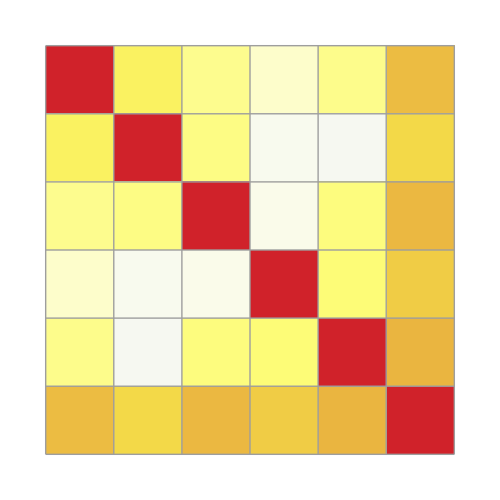
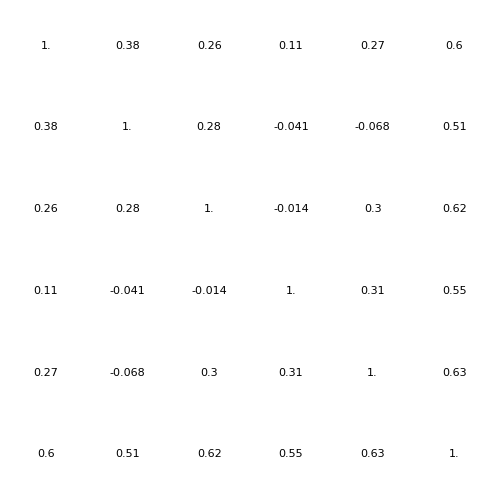
-Graphics-
-Graphics--Graphics--Graphics-

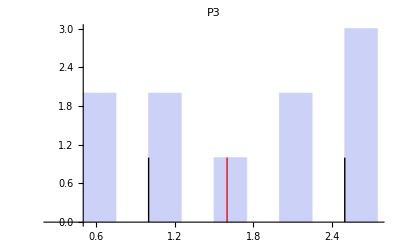
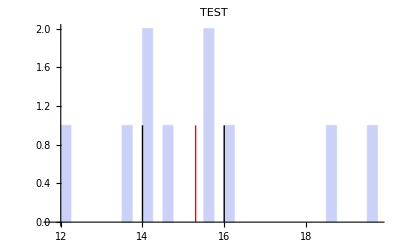
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

-Graphics-

```mathematica
(*labels for the correlation array*)
labels={P1,P2,P3,P4,P5,TEST};
(*Fancy,picture*)
Column[{GraphicsRow[labels,ImageSize->500,Frame->All],Row[{GraphicsColumn[labels,ImageSize->83,Frame->All],Overlay[{ArrayPlot[corr,ColorFunction->(ColorData["TemperatureMap"][(1+#)/2]&),Frame->None,Mesh->True,PlotRangePadding->0,ImageSize->500,ColorFunctionScaling->False],GraphicsGrid[Map[NumberForm[#,2]&,corr,{2}],ImageSize->500]}]}]},Alignment->Right,Spacings->0]
(*histograms for each problem & test as a whole*)
histograms={};
For[i=1,i≤6,i++,
histograms=Append[histograms,Histogram[score[[i]],{.25},Epilog->{Directive[{Thick,Red}],Line[{{Mean[score[[i]]],0},{Mean[score[[i]]],1}}],{Directive[{Thick,Black}],Line[{{Quartiles[score[[i]]][[1]],0},{Quartiles[score[[i]]][[1]],1}}],Line[{{Quartiles[score[[i]]][[3]],0},{Quartiles[score[[i]]][[3]],1}}]}},PlotLabel->labels[[i]]]];
]
histograms
histograms[[6]]
```

```mathematica
(*conclusion: adjust 3 by half*)
```